## Fixed M_Z'=10 TeV, Fixed Brane parameter = 0.1, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 ( (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime10=10;
MassNu=0.1;
CvL01=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.1)
```

0.099871

```mathematica
Zprime10decayfixedmass01[CvR_]:=MassZprime10/(12π)(1/4(CvL01+CvR)^2+1/4(CvL01-CvR)^2+2(MassNu/MassZprime10)^2(1/4(CvL01+CvR)^2-1/2(CvL01+CvR)^2))√(1-4(MassNu/MassZprime10)^2)*10^3
```

```mathematica
Zprime10decayfixedmass01[0.0]
Zprime10decayfixedmass01[0.1]
Zprime10decayfixedmass01[0.2]
Zprime10decayfixedmass01[0.3]
Zprime10decayfixedmass01[0.4]
Zprime10decayfixedmass01[0.5]
Zprime10decayfixedmass01[0.6]
Zprime10decayfixedmass01[0.7]
Zprime10decayfixedmass01[0.8]
Zprime10decayfixedmass01[0.9]
Zprime10decayfixedmass01[1.0]
```

1.32248

2.6481

6.62552

13.2547

22.5357

34.4685

49.053

66.2894

86.1775

108.717

133.909

```mathematica
DecayTableFixed1001=TableForm[{{0.0,Zprime10decayfixedmass01[0.0]},{0.1,Zprime10decayfixedmass01[0.1]},{0.2,Zprime10decayfixedmass01[0.2]},{0.3,Zprime10decayfixedmass01[0.3]},{0.4,Zprime10decayfixedmass01[0.4]},{0.5,Zprime10decayfixedmass01[0.5]},{0.6,Zprime10decayfixedmass01[0.6]},{0.7,Zprime10decayfixedmass01[0.7]},{0.8,Zprime10decayfixedmass01[0.8]},{0.9,Zprime10decayfixedmass01[0.9]},{1.0,Zprime10decayfixedmass01[1.0]}},TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 1.32248
0.1 | 2.6481
0.2 | 6.62552
0.3 | 13.2547
0.4 | 22.5357
0.5 | 34.4685
0.6 | 49.053
0.7 | 66.2894
0.8 | 86.1775
0.9 | 108.717
1. | 133.909

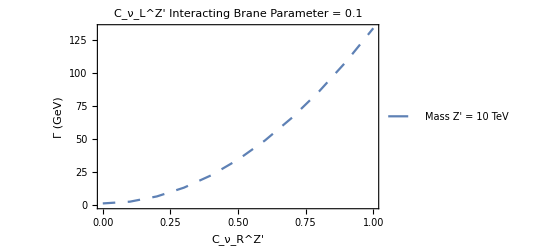

```mathematica
PlotZprimeDecayFixed1001=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Mass Z' = 10 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm["C_ν_L^Z' Interacting Brane Parameter = 0.1"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

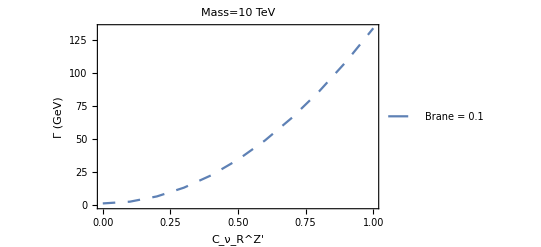

```mathematica
PlotZprimeDecayFixed1001B=ListPlot[%%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Brane = 0.1"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 10 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

## Fixed M_Z'=8 TeV, Fixed Brane parameter = 0.1, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime8=8;
MassNu=0.1;
CvL01=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.1)
```

0.099871

```mathematica
Zprime8decayfixedmass01[CvR_]:=MassZprime8/(12π)(1/4(CvL01+CvR)^2+1/4(CvL01-CvR)^2+2(MassNu/MassZprime8)^2(1/4(CvL01+CvR)^2-1/2(CvL01+CvR)^2))√(1-4(MassNu/MassZprime8)^2)*10^3
```

```mathematica
Zprime8decayfixedmass01[0.0]
Zprime8decayfixedmass01[0.1]
Zprime8decayfixedmass01[0.2]
Zprime8decayfixedmass01[0.3]
Zprime8decayfixedmass01[0.4]
Zprime8decayfixedmass01[0.5]
Zprime8decayfixedmass01[0.6]
Zprime8decayfixedmass01[0.7]
Zprime8decayfixedmass01[0.8]
Zprime8decayfixedmass01[0.9]
Zprime8decayfixedmass01[1.0]
```

1.0578

2.11801

5.29928

10.6016

18.025

27.5695

39.2351

53.0217

68.9294

86.9582

107.108

```mathematica
DecayTableFixed801=TableForm[{{0.0,Zprime8decayfixedmass01[0.0]},{0.1,Zprime8decayfixedmass01[0.1]},{0.2,Zprime8decayfixedmass01[0.2]},{0.3,Zprime8decayfixedmass01[0.3]},{0.4,Zprime8decayfixedmass01[0.4]},{0.5,Zprime8decayfixedmass01[0.5]},{0.6,Zprime8decayfixedmass01[0.6]},{0.7,Zprime8decayfixedmass01[0.7]},{0.8,Zprime8decayfixedmass01[0.8]},{0.9,Zprime8decayfixedmass01[0.9]},{1.0,Zprime8decayfixedmass01[1.0]}},TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 1.0578
0.1 | 2.11801
0.2 | 5.29928
0.3 | 10.6016
0.4 | 18.025
0.5 | 27.5695
0.6 | 39.2351
0.7 | 53.0217
0.8 | 68.9294
0.9 | 86.9582
1. | 107.108

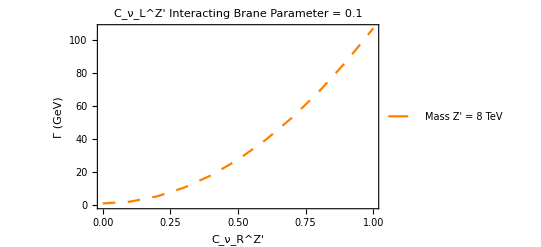

```mathematica
PlotZprimeDecayFixed801=ListPlot[%, Joined-> True,PlotStyle->{Orange, Dashing[Medium]},PlotLegends->{"Mass Z' = 8 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm["C_ν_L^Z'  Interacting Brane Parameter = 0.1"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

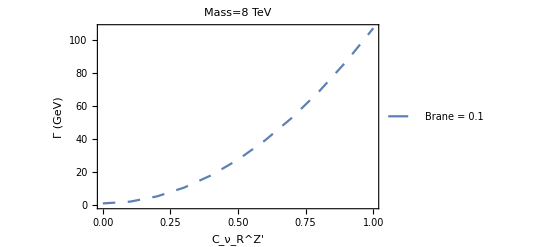

```mathematica
PlotZprimeDecayFixed801B=ListPlot[%%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Brane = 0.1"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 8 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

## Fixed M_Z'=5 TeV, Fixed Brane parameter = 0.1, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime5=5;
MassNu=0.1;
CvL01=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.1)
```

0.099871

```mathematica
Zprime5decayfixedmass01[CvR_]:=MassZprime5/(12π)(1/4(CvL01+CvR)^2+1/4(CvL01-CvR)^2+2(MassNu/MassZprime5)^2(1/4(CvL01+CvR)^2-1/2(CvL01+CvR)^2))√(1-4(MassNu/MassZprime5)^2)*10^3
```

```mathematica
Zprime5decayfixedmass01[0.0]
Zprime5decayfixedmass01[0.1]
Zprime5decayfixedmass01[0.2]
Zprime5decayfixedmass01[0.3]
Zprime5decayfixedmass01[0.4]
Zprime5decayfixedmass01[0.5]
Zprime5decayfixedmass01[0.6]
Zprime5decayfixedmass01[0.7]
Zprime5decayfixedmass01[0.8]
Zprime5decayfixedmass01[0.9]
Zprime5decayfixedmass01[1.0]
```

0.660643

1.32246

3.30898

6.6202

11.2561

17.2167

24.5021

33.1121

43.0468

54.3062

66.8903

```mathematica
DecayTableFixed501=TableForm[{{0.0,Zprime5decayfixedmass01[0.0]},{0.1,Zprime5decayfixedmass01[0.1]},{0.2,Zprime5decayfixedmass01[0.2]},{0.3,Zprime5decayfixedmass01[0.3]},{0.4,Zprime5decayfixedmass01[0.4]},{0.5,Zprime5decayfixedmass01[0.5]},{0.6,Zprime5decayfixedmass01[0.6]},{0.7,Zprime5decayfixedmass01[0.7]},{0.8,Zprime5decayfixedmass01[0.8]},{0.9,Zprime5decayfixedmass01[0.9]},{1.0,Zprime5decayfixedmass01[1.0]}},TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 0.660643
0.1 | 1.32246
0.2 | 3.30898
0.3 | 6.6202
0.4 | 11.2561
0.5 | 17.2167
0.6 | 24.5021
0.7 | 33.1121
0.8 | 43.0468
0.9 | 54.3062
1. | 66.8903

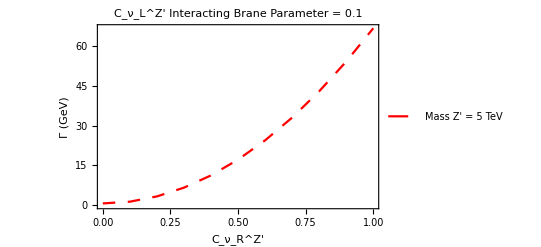

```mathematica
PlotZprimeDecayFixed501=ListPlot[%, Joined-> True,PlotStyle->{Red, Dashing[Medium]},PlotLegends->{"Mass Z' = 5 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm["C_ν_L^Z'  Interacting Brane Parameter = 0.1"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

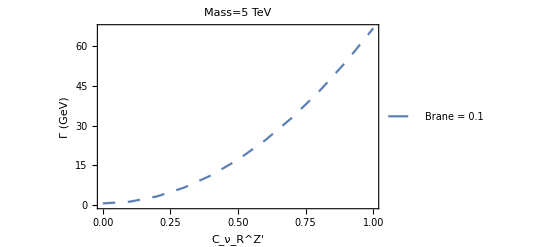

```mathematica
PlotZprimeDecayFixed501B=ListPlot[%%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Brane = 0.1"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 5 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

## OverLay

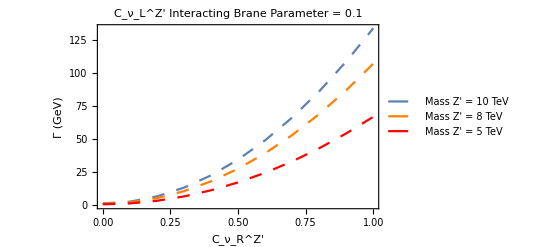

```mathematica
Show[PlotZprimeDecayFixed1001,PlotZprimeDecayFixed801,PlotZprimeDecayFixed501]
```